```mathematica
ClearAll["Global`*"];

M=1.;
k0=0.1;
lam0=0.1;
ell0=2;
mass0=0.2;

f[r_?NumericQ]:=1/(1-k0)-2 M/r+(lam0/r) Log[r/lam0];

fp[r_?NumericQ]:=2 M/r^2+(lam0/r^2) (1-Log[r/lam0]);

Veff[r_?NumericQ]:=f[r] (ell0 (ell0+1)/r^2+fp[r]/r+mass0^2);
```

```mathematica
rh=r/. FindRoot[f[r]==0,{r,1.5}];

N[rh,12]
f[rh]
```

1.55314

-5.55112×10^-17

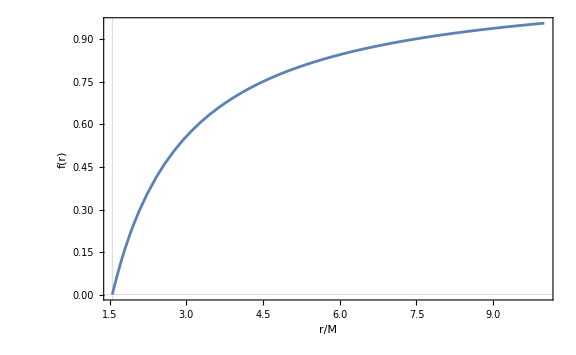

```mathematica
Plot[f[r],{r,rh+10^-4,10},Frame->True,FrameLabel->{"r/M","f(r)"},PlotRange->All,GridLines->{{rh},{0}},ImageSize->Large]
```

## tortoise coordinate transform

```mathematica
rRef=10.;

rs[r_?NumericQ]:=NIntegrate[1/f[x],{x,rRef,r},Method->{"GlobalAdaptive","SymbolicProcessing"->0},WorkingPrecision->30,AccuracyGoal->15,PrecisionGoal->15];
```

```mathematica
rs[10.]
```

0

```mathematica
Table[{r,rs[r]},{r,{rh+0.001,rh+0.01,2.,3.,5.,10.,20.,50.}}]//TableForm
```

1.55414 | -19.409266704203769296994630885
1.56314 | -16.3590763754780597983116424845
2. | -10.9564164376607986600522301674
3. | -8.52611220261702805217150844301
5. | -5.61572394054983121356528576399
10. | 0
20. | 9.9374179436060901796808429015
50. | 38.0415361039324853067208954574

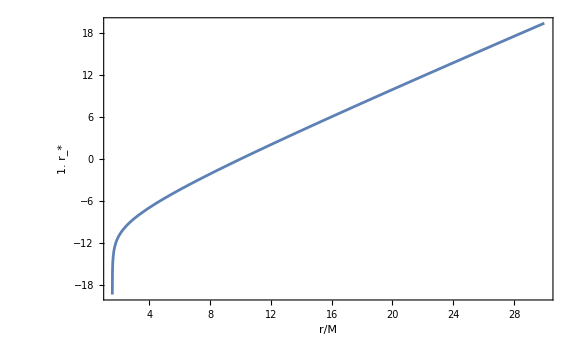

```mathematica
Plot[Evaluate[rs[r]],{r,rh+0.001,30},Frame->True,FrameLabel->{"r/M",Subscript["r","*"]/M},PlotRange->All,ImageSize->Large]
```

```mathematica
N[rh,12]
```

1.55314

```mathematica
Table[{r,rs[r]},{r,{rh+0.001,rh+0.01,2.,3.,5.,10.,20.,50.}}]//TableForm
```

1.55414 | -19.409266704203769296994630885
1.56314 | -16.3590763754780597983116424845
2. | -10.9564164376607986600522301674
3. | -8.52611220261702805217150844301
5. | -5.61572394054983121356528576399
10. | 0
20. | 9.9374179436060901796808429015
50. | 38.0415361039324853067208954574

```mathematica
ClearAll[rr,rOfRs];

rsMin=-30.;
rsMax=50.;
rRef=10.;

rSolution=NDSolveValue[{rr'[x]==f[rr[x]],rr[0]==rRef},rr,{x,rsMin,rsMax},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}},AccuracyGoal->12,PrecisionGoal->10];

rOfRs[x_?NumericQ]:=rSolution[x];
```

```mathematica
ClearAll[Vstar,VxFinal,rOfXFinal,rsPeak];
```

```mathematica
Vstar[s_?NumericQ]:=Veff[rOfRs[s]];

peakResult=NMaximize[{Vstar[s],-20.<s<5.},s];

rsPeak=s/. peakResult[[2]];

N[rsPeak,10]
```

-10.0161

```mathematica
Table[{rs0,rOfRs[rs0]},{rs0,{-30.,-20.,-10.,-5.,0.,5.,10.,20.,30.,50.}}]//TableForm
```

-30. | 1.55314
-20. | 1.55378
-10. | 2.30563
-5. | 5.49572
0. | 10.
5. | 14.9369
10. | 20.0649
20. | 30.5951
30. | 41.3102
50. | 62.9965

```mathematica
rOfRs[-10.9564164377]
```

2.00004

```mathematica
{rOfRs[-10.9564164377],rOfRs[-5.61572394055],rOfRs[0.],rOfRs[9.93741794361]}
```

{2.00004,4.99999,10.,20.}

```mathematica
Veff[r_?NumericQ]:=f[r] (ell0 (ell0+1)/r^2+fp[r]/r+mass0^2);
```

```mathematica
ClearAll[Vstar];

Vstar[x_?NumericQ]:=Veff[rOfRs[x]];
```

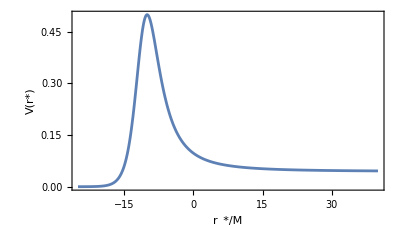

```mathematica
Plot[Vstar[x],{x,-25,40},Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(*\)]\)/M","V(r*)"},PlotRange->All,AspectRatio->9/16]
```

```mathematica
peakStar=NMaximize[{Vstar[x],-20<x<5},x];

rsPeak=x/. peakStar[[2]];
rPeakTD=rOfRs[rsPeak];
vPeak=Vstar[rsPeak];

{rsPeak,rPeakTD,vPeak}
```

{-10.0161,2.29951,0.499185}

## td setup

```mathematica
(* =====================================*)(*FINAL TD SETUP FOR REVIEWER COMMENT 2*)(* =====================================*)ClearAll[VxFinal,rOfXFinal];

(*Shift tortoise coordinate so that potential peak is at x=0*)
rOfXFinal[x_?NumericQ]:=rOfRs[x+rsPeak];
VxFinal[x_?NumericQ]:=Vstar[x+rsPeak];

(*Quick check*)
N[{rOfXFinal[0.],VxFinal[0.]},10]
```

{2.29951,0.499185}

```mathematica
(* ==============================*)(*FIXED TD PARAMETERS*)(* ==============================*)uMinTD=0.;
uMaxTD=120.;

vMinTD=0.;
vMaxTD=120.;

A0TD=1.;

(*Gaussian initial pulse*)
vcTD=20.;
sigmaTD=3.;

(*Fixed extraction point*)
xObsTD=10.*2;
```

```mathematica
ClearAll[TDEvolve];

TDEvolve[hTD_?NumericQ]:=Module[{Nu,Nv,uGrid,vGrid,psi,i,j,u0,v0,xC,VC,psiS,psiE,psiW,shiftObs,waveData},Nu=Round[(uMaxTD-uMinTD)/hTD];
Nv=Round[(vMaxTD-vMinTD)/hTD];
uGrid=Table[uMinTD+i hTD,{i,0,Nu}];
vGrid=Table[vMinTD+j hTD,{j,0,Nv}];
psi=ConstantArray[0.,{Nu+1,Nv+1}];
(*------------------------------*)(*INITIAL DATA ON u=0*)(*------------------------------*)Do[psi[[1,j+1]]=A0TD Exp[-(vGrid[[j+1]]-vcTD)^2/(2 sigmaTD^2)],{j,0,Nv}];
(*------------------------------*)(*INITIAL DATA ON v=0*)(*------------------------------*)Do[psi[[i+1,1]]=0.,{i,0,Nu}];
(*------------------------------*)(*CHARACTERISTIC EVOLUTION*)(*------------------------------*)Do[Do[u0=uGrid[[i]];
v0=vGrid[[j]];
(*Cell-center tortoise coordinate*)xC=(v0-u0)/2.;
VC=VxFinal[xC];
psiS=psi[[i,j]];
psiE=psi[[i,j+1]];
psiW=psi[[i+1,j]];
psi[[i+1,j+1]]=psiE+psiW-psiS-(hTD^2/8.) VC (psiE+psiW);,{j,1,Nv}],{i,1,Nu}];
(*------------------------------*)(*EXTRACTION AT FIXED xObsTD*)(*------------------------------*)shiftObs=Round[2 xObsTD/hTD];
waveData=Table[Module[{jj,uVal,vVal,tVal},jj=i+shiftObs;
If[jj<=Nv,uVal=uGrid[[i+1]];
vVal=vGrid[[jj+1]];
tVal=(uVal+vVal)/2.;
{tVal,psi[[i+1,jj+1]]},Nothing]],{i,0,Nu}];
waveData]
```

```mathematica
wave05=TDEvolve[0.5];
```

InterpolatingFunction::dmval: Input value {-30.0161} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-30.2661} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-30.0161} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

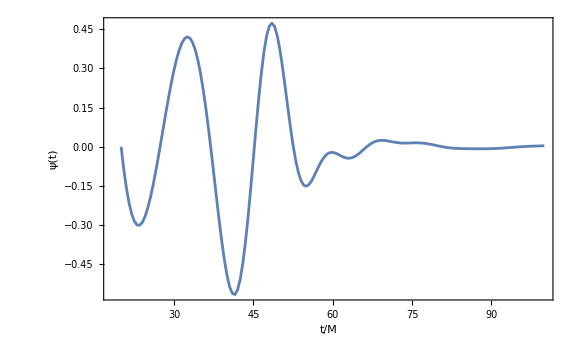

```mathematica
ListLinePlot[wave05,Frame->True,FrameLabel->{"t/M","ψ(t)"},PlotRange->All,ImageSize->Large]
```

```mathematica
wave025=TDEvolve[0.25];

wave0125=TDEvolve[0.125];
```

InterpolatingFunction::dmval: Input value {-30.0161} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-30.1411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-30.0161} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-30.0161} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-30.0786} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-30.0161} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

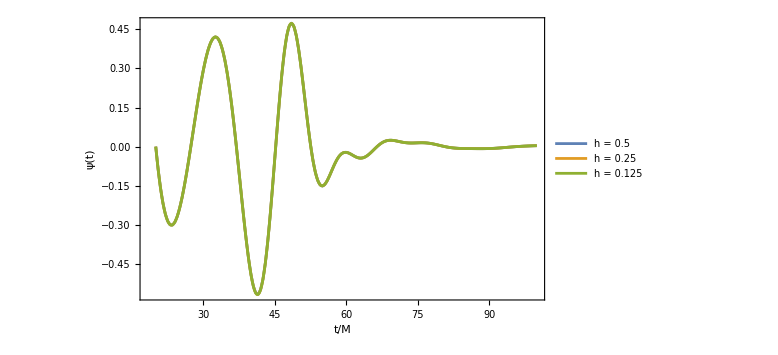

```mathematica
ListLinePlot[{wave05,wave025,wave0125},Frame->True,FrameLabel->{"t/M","ψ(t)"},PlotLegends->{"h = 0.5","h = 0.25","h = 0.125"},PlotRange->All,ImageSize->Large]
```

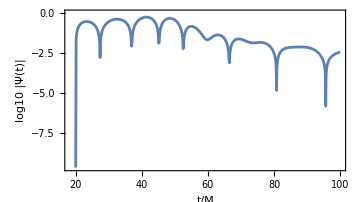

```mathematica
ListLinePlot[Select[({#[[1]],Log10[Abs[#[[2]]]]}&/@wave0125),NumberQ[#[[2]]]&&#[[2]]>-12&],Frame->True,FrameLabel->{"t/M","log10 |Ψ(t)|"},PlotRange->All,ImageSize->Medium,AspectRatio->9/16]
```

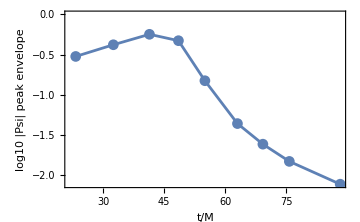

```mathematica
(*high-resolution signed waveform*)times=wave0125[[All,1]];
vals=wave0125[[All,2]];

(*local maxima of|Psi|*)
peakIndices=Select[Range[2,Length[vals]-1],Abs[vals[[#]]]>Abs[vals[[#-1]]]&&Abs[vals[[#]]]>Abs[vals[[#+1]]]&];

envelopeData=Table[{times[[i]],Log10[Abs[vals[[i]]]]},{i,peakIndices}];

ListPlot[envelopeData,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"t/M","log10 |Psi| peak envelope"},PlotRange->All,ImageSize->Medium]
```

```mathematica
dtTest=0.125;

testData=Table[{t,Exp[-0.142071 (t-55.)]*Cos[0.684184 (t-55.)]},{t,55.,76.,dtTest}];
```

```mathematica
mpTest=matrixPencilQNM[testData,55.,76.,2];

mpTest["Exponents"]
```

{-0.142071+0.684184 ⅈ,-0.142071-0.684184 ⅈ}

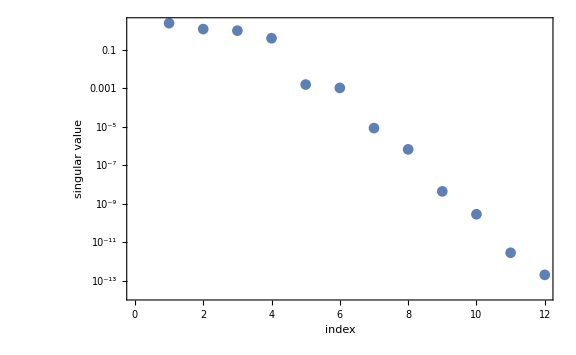

```mathematica
fitData=Select[wave0125,55.<=#[[1]]<=76.&];
y=fitData[[All,2]];

n=Length[y];
L=Floor[n/2];

Y0=Table[y[[i+j-1]],{i,1,n-L},{j,1,L}];

sv=SingularValueList[N[Y0]];

ListLogPlot[sv,Frame->True,FrameLabel->{"index","singular value"},PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Take[sv,10]
```

{2.32745,1.15128,0.954437,0.385593,0.00152725,0.00101833,8.36071×10^-6,6.61334×10^-7,4.36931×10^-9,2.84112×10^-10}

```mathematica
mp4=matrixPencilQNM[wave0125,55.,76.,4];

mp4["Exponents"]
```

{-0.0856988+0.198391 ⅈ,-0.0856988-0.198391 ⅈ,-0.147647+0.681962 ⅈ,-0.147647-0.681962 ⅈ}

```mathematica
modes4=Select[mp4["Exponents"],Re[#]<0&&Abs[Im[#]]>10^-6&];

modes4
```

{-0.0856988+0.198391 ⅈ,-0.0856988-0.198391 ⅈ,-0.147647+0.681962 ⅈ,-0.147647-0.681962 ⅈ}

```mathematica
Table[{-Re[m],Abs[Im[m]]},{m,modes4}]
```

{{0.0856988,0.198391},{0.0856988,0.198391},{0.147647,0.681962},{0.147647,0.681962}}

```mathematica
windows={{52.,73.},{53.,74.},{54.,75.},{55.,76.},{56.,77.},{57.,78.},{58.,79.}};

windowModes=Table[Module[{mpTmp,modes},mpTmp=matrixPencilQNM[wave0125,win[[1]],win[[2]],4];
modes=Select[mpTmp["Exponents"],Re[#]<0&&Im[#]>0&];
{win,Table[{"gamma"->-Re[m],"omegaR"->Im[m]},{m,modes}]}],{win,windows}];

windowModes//TableForm
```

52.
73. | gamma→0.104616 | omegaR→0.232647
gamma→0.166991 | omegaR→0.658199
53.
74. | gamma→0.0914969 | omegaR→0.216322
gamma→0.164146 | omegaR→0.676407
54.
75. | gamma→0.0863571 | omegaR→0.204012
gamma→0.153577 | omegaR→0.683571
55.
76. | gamma→0.0856988 | omegaR→0.198391
gamma→0.147647 | omegaR→0.681962
56.
77. | gamma→0.0862047 | omegaR→0.198616
gamma→0.148081 | omegaR→0.680683
57.
78. | gamma→0.0859153 | omegaR→0.202091
gamma→0.149455 | omegaR→0.683488
58.
79. | gamma→0.0843983 | omegaR→0.206381
gamma→0.147566 | omegaR→0.687925

```mathematica
ClearAll[getOscillatoryModes];

getOscillatoryModes[data_,t1_,t2_]:=Module[{mpTmp,modes},mpTmp=matrixPencilQNM[data,t1,t2,4];
modes=Select[mpTmp["Exponents"],Re[#]<0&&Im[#]>0&];
SortBy[Table[{-Re[m],Im[m]},{m,modes}],Last]]
```

```mathematica
gridModes={{"h = 0.5",getOscillatoryModes[wave05,55.,76.]},{"h = 0.25",getOscillatoryModes[wave025,55.,76.]},{"h = 0.125",getOscillatoryModes[wave0125,55.,76.]}};

gridModes//TableForm
```

h = 0.5 | 0.0858845 | 0.198512
0.147424 | 0.682939
h = 0.25 | 0.0857386 | 0.198494
0.147665 | 0.68221
h = 0.125 | 0.0856988 | 0.198391
0.147647 | 0.681962

```mathematica
ClearAll[matrixPencilReconstruction];

matrixPencilReconstruction[data_,t1_,t2_,rank_:4]:=Module[{fitData,times,y,t0,mp,sModes,design,amps,yFit,residual,rmsResidual,relativeRMS},fitData=Select[data,t1<=#[[1]]<=t2&];
times=fitData[[All,1]];
y=fitData[[All,2]];
t0=First[times];
mp=matrixPencilQNM[data,t1,t2,rank];
sModes=mp["Exponents"];
(*modal model:Psi(t)=Sum[A_j Exp[s_j (t-t0)]]*)design=Table[Exp[sModes[[j]] (times[[i]]-t0)],{i,Length[times]},{j,Length[sModes]}];
(*least-squares amplitudes*)amps=LeastSquares[design,y];
yFit=Re[design.amps];
residual=y-yFit;
rmsResidual=Sqrt[Mean[residual^2]];
relativeRMS=rmsResidual/Sqrt[Mean[y^2]];
<|"Modes"->sModes,"Amplitudes"->amps,"FitData"->Transpose[{times,yFit}],"ResidualData"->Transpose[{times,residual}],"RMSResidual"->rmsResidual,"RelativeRMS"->relativeRMS|>]
```

```mathematica
rec=matrixPencilReconstruction[wave0125,55.,76.,4];

rec["RMSResidual"]
rec["RelativeRMS"]
```

0.0000616242

0.00125509

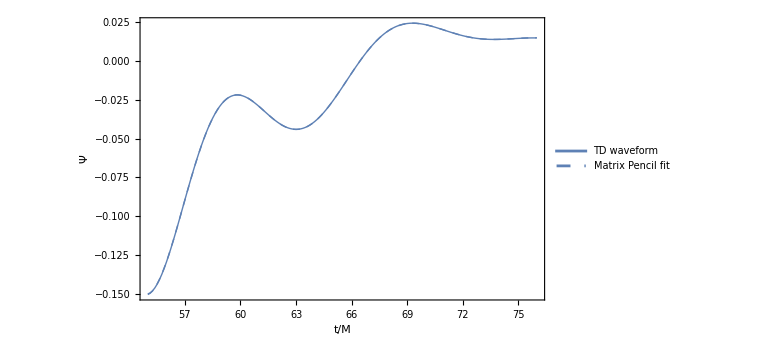

```mathematica
Show[ListLinePlot[Select[wave0125,55.<=#[[1]]<=76.&],PlotStyle->{Thick},PlotLegends->{"TD waveform"}],ListLinePlot[rec["FitData"],PlotStyle->{Dashed,Thick},PlotLegends->{"Matrix Pencil fit"}],Frame->True,FrameLabel->{"t/M","Ψ"},PlotRange->All,ImageSize->Large]
```

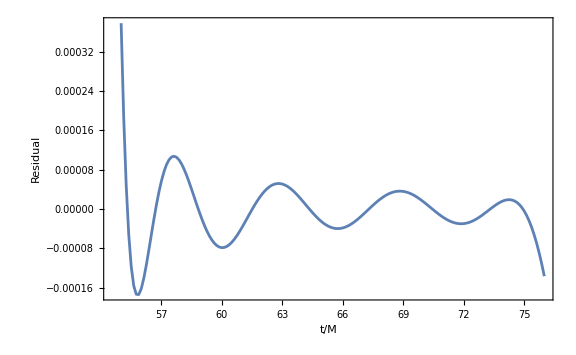

```mathematica
ListLinePlot[rec["ResidualData"],Frame->True,FrameLabel->{"t/M","Residual"},PlotRange->All,ImageSize->Large]
```

```mathematica
rec["RMSResidual"]
rec["RelativeRMS"]
```

0.0000616242

0.00125509

```mathematica
N[rOfXFinal[20.],12]
```

20.0482

```mathematica
ClearAll[waveDifference];

waveDifference[dataCoarse_,dataFine_,t1_,t2_]:=Module[{coarse,fineInterp,diff},coarse=Select[dataCoarse,t1<=#[[1]]<=t2&];
fineInterp=Interpolation[dataFine,InterpolationOrder->1];
diff=Table[coarse[[i,2]]-fineInterp[coarse[[i,1]]],{i,Length[coarse]}];
Sqrt[Mean[diff^2]]]
```

```mathematica
e1=waveDifference[wave05,wave025,20.,100.];

e2=waveDifference[wave025,wave0125,20.,100.];

{e1,e2,e1/e2,Log[2,e1/e2]}
```

{0.000310532,0.0000773908,4.01252,2.00451}

```mathematica
envelopeData
```

{{23.25,-0.521481},{32.5,-0.376138},{41.375,-0.246279},{48.5,-0.325537},{55.,-0.823203},{63.,-1.356},{69.25,-1.612},{75.75,-1.82603},{88.25,-2.10938}}

```mathematica
xObsTD
First[wave05]
Last[wave05]
```

20.

{20.,2.23363×10^-10}

{100.,0.00370059}

```mathematica
{First[wave05],Last[wave05]}
```

{{10.,1.},{110.,-0.0000821992}}

```mathematica
Max[Abs[wave05[[All,2]]]]
```

1.

## Signed wave form for project

```mathematica
<<MaTeX``
```

Get::noopen: Cannot open MaTeX.

$Failed

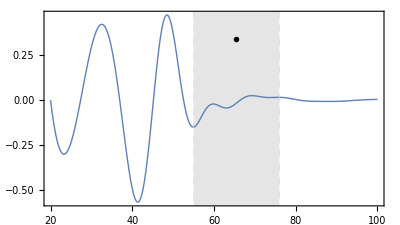

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6a.pdf

```mathematica
Needs["MaTeX`"];

fig6a=ListLinePlot[wave0125,Frame->True,Axes->False,FrameLabel->{MaTeX["t/M",Magnification->1.4],MaTeX["\\Phi(t)",Magnification->1.4]},PlotRange->{{20,100},All},PlotStyle->Thick,AspectRatio->9/16,BaseStyle->{FontFamily->"Times",FontSize->13},Prolog->{Opacity[0.10],Rectangle[{55,-1},{76,1}]},GridLines->{{55,76},None},GridLinesStyle->Directive[Dashed],Epilog->{Text[MaTeX["\\mathbf{(a)}",Magnification->1.25],Scaled[{0.10,0.90}]],Text[MaTeX["55M\\leq t\\leq 76M",Magnification->1.1],{65.5,0.34}]}];

fig6a
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6a.pdf",fig6a,"PDF"]
```

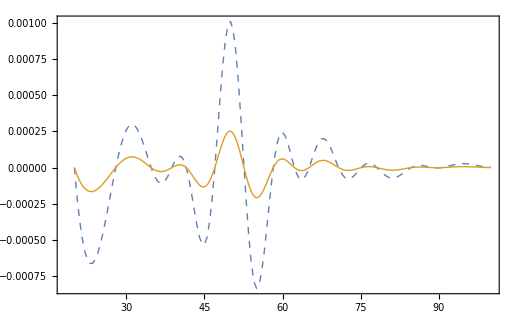

```mathematica
interp025=Interpolation[wave025,InterpolationOrder->1];
interp0125=Interpolation[wave0125,InterpolationOrder->1];

diff1=Table[{wave05[[i,1]],wave05[[i,2]]-interp025[wave05[[i,1]]]},{i,Length[wave05]}];

diff2=Table[{wave025[[i,1]],wave025[[i,2]]-interp0125[wave025[[i,1]]]},{i,Length[wave025]}];


diff1Plot=Select[diff1,20<=#[[1]]<=100&];
diff2Plot=Select[diff2,20<=#[[1]]<=100&];


fig6b=ListLinePlot[{diff1Plot,diff2Plot},Frame->True,Axes->False,FrameLabel->{MaTeX["t/M",Magnification->1.4],MaTeX["\\Delta\\Psi(t)",Magnification->1.4]},PlotStyle->{Directive[Thick,Dashed],Directive[Thick]},PlotLegends->Placed[{MaTeX["\\Psi_{0.5}-\\Psi_{0.25}",Magnification->1.0],MaTeX["\\Psi_{0.25}-\\Psi_{0.125}",Magnification->1.0]},{0.76,0.78}],Epilog->{Text[MaTeX["p=2.0045",Magnification->1.15],Scaled[{0.78,0.23}]]},BaseStyle->{FontFamily->"Times",FontSize->13},PlotRange->All,ImageSize->520];

fig6b
```

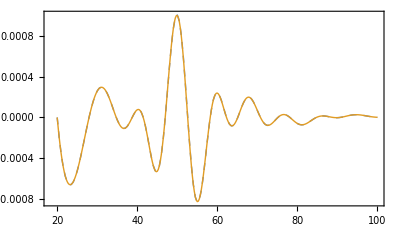

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6Scaled.pdf

```mathematica
diff2Scaled={#[[1]],4 #[[2]]}&/@diff2Plot;

fig6bScaled=ListLinePlot[{diff1Plot,diff2Scaled},Frame->True,Axes->False,FrameLabel->{MaTeX["t/M",Magnification->1.4],MaTeX["\\Delta\\Phi(t)",Magnification->1.4]},PlotStyle->{Directive[Thick,Dashed],Directive[Thick]},PlotLegends->Placed[{MaTeX["\\Phi_{0.5}-\\Phi_{0.25}",Magnification->1.0],MaTeX["4\\left(\\Phi_{0.25}-\\Phi_{0.125}\\right)",Magnification->1.0]},{0.73,0.78}],Epilog->{Text[MaTeX["\\mathbf{(b)}",Magnification->1.25],Scaled[{0.10,0.90}]],Text[MaTeX["p=2.0045",Magnification->1.15],Scaled[{0.78,0.23}]]},BaseStyle->{FontFamily->"Times",FontSize->13},PlotRange->All,AspectRatio->9/16];

fig6bScaled

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6Scaled.pdf",fig6bScaled,"PDF"]
```

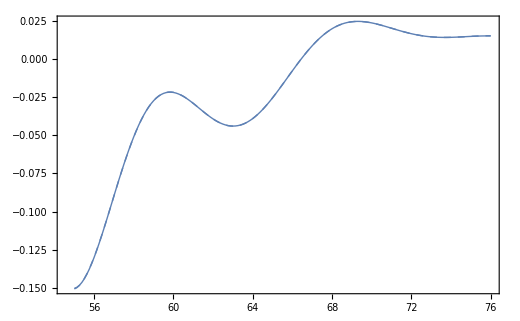

```mathematica
Needs["MaTeX`"];

tdWindow=Select[wave0125,55.<=#[[1]]<=76.&];

fitWindow=rec["FitData"];

fig6c=Show[ListLinePlot[tdWindow,PlotStyle->Directive[Thick],PlotRange->All],ListLinePlot[fitWindow,PlotStyle->Directive[Thick,Dashed]],Frame->True,Axes->False,FrameLabel->{MaTeX["t/M",Magnification->1.4],MaTeX["\\Psi(t)",Magnification->1.4]},PlotLegends->Placed[{MaTeX["\\mathrm{TD\\ waveform}",Magnification->1.0],MaTeX["\\mathrm{Matrix\\ Pencil\\ fit}",Magnification->1.0]},{0.72,0.78}],Epilog->{Text[MaTeX["\\omega_{\\mathrm{TD}}=0.68196-0.14765\\,i",Magnification->1.05],Scaled[{0.60,0.23}]],Text[MaTeX["\\epsilon_{\\mathrm{RMS}}=1.26\\times10^{-3}",Magnification->1.05],Scaled[{0.60,0.14}]]},BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->520];

fig6c
```

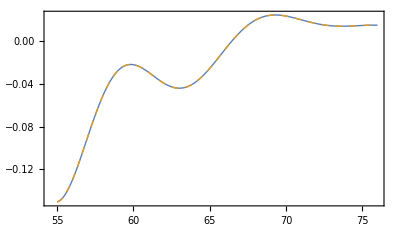

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6c.pdf

```mathematica
fig6c=ListLinePlot[{tdWindow,fitWindow},Frame->True,Axes->False,FrameLabel->{MaTeX["t/M",Magnification->1.4],MaTeX["\\Phi(t)",Magnification->1.4]},PlotStyle->{Directive[Thick],Directive[Thick,Dashed]},PlotLegends->Placed[{MaTeX["\\mathrm{TD\\ waveform}",Magnification->1.0],MaTeX["\\mathrm{Matrix\\ Pencil\\ fit}",Magnification->1.0]},{0.72,0.78}],Epilog->{(*Panel label*)Text[MaTeX["\\mathbf{(c)}",Magnification->1.25],Scaled[{0.10,0.90}]],(*Extracted QNM*)Text[MaTeX["\\omega_{\\mathrm{TD}}=0.68196-0.14765\\,i",Magnification->1.05],Scaled[{0.60,0.22}]],(*Relative RMS residual*)Text[MaTeX["\\epsilon_{\\mathrm{rel}}=1.26\\times10^{-3}",Magnification->1.05],Scaled[{0.60,0.13}]]},PlotRange->All,BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->9/16];

fig6c

Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6c.pdf",fig6c,"PDF"]
```

```mathematica
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6Final.pdf",fig6Final,"PDF"]
```

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/fig6Final.pdf